## Johns Hopkins Data

Note:  To avoid day-of-the-week effects and noisy data, both case counts and recombination events were totaled per week.

### [Enter]

```mathematica
startafter="2020-01-21";(*First date of case data*)
```

```mathematica
endatdate="2023-02-14"; (*Last date of recombinants, plus one to complete the week*)
```

```mathematica
endatdate2="2/14/23"; (*In format of Johns Hopkins*)
```

```mathematica
curdate[x_]:=InputForm[DateObject[x]-DateObject[startafter]][[1,1]];
```

```mathematica
maxdate=curdate[endatdate];
```

```mathematica
xaxis={{curdate["2020-01-01"],"Jan 2020"},{curdate["2020-07-01"],"Jul 2020"},{curdate["2021-01-01"],"Jan 2021"},{curdate["2021-07-01"],"Jul 2021"},{curdate["2022-01-01"],"Jan 2022"},{curdate["2022-07-01"],"Jul 2022"},{curdate["2023-01-01"],"Jan 2023"},{curdate["2023-07-01"],"Jul 2023"},{curdate["2024-01-01"],"Jan 2024"},{curdate["2024-07-01"],"Jul 2024"},{curdate["2025-01-01"],"Jan 2025"}};
```

### Case number data - weekly

Imported from Johns Hopkins’ time series data
https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_time_series

```mathematica
global=Import["/Users/otto/Dropbox/COVID19/Recombinants/sc2ts/GlobalTrends/time_series_covid19_confirmed_global.csv","CSV"];
```

```mathematica
header=global[[1]];
```

We’ll trim the data

```mathematica
maxpos=Position[header,endatdate2][[1,1]]
```

1124

```mathematica
caldates=header[[5;;maxpos]];
```

```mathematica
cumcases=Total[global[[2;;All,5;;maxpos]]];
```

```mathematica
cases=Join[{cumcases[[1]]},Table[cumcases[[i]]-cumcases[[i-1]],{i,2,Length[cumcases]}]];
```

The date format for Johns Hopkins’ is different (MM/DD/YY), so we specify it in the same format to get the current date:

```mathematica
curdateJH[x_]:=InputForm[DateObject[{x,{"Month","/","Day","/","YearShort"}},"Day"]-DateObject[startafter]][[1,1]];
```

```mathematica
dates=Table[curdateJH[caldates[[i]]],{i,1,Length[caldates]}];
```

All dates are included:

```mathematica
UniqueElements[{dates,Table[i,{i,1,Length[dates]}]}]
```

{{},{}}

And there are no dates without cases:

```mathematica
Min[cases]
```

100

Grouping by week:

```mathematica
cases=Total /@ Partition[cases,7]//N
```

{5580.,18319.,20915.,30341.,5257.,12582.,26057.,79288.,225255.,445777.,528515.,606340.,567747.,549134.,559507.,591030.,633095.,696689.,804793.,852224.,935488.,1.05669×10^6,1.22476×10^6,1.37651×10^6,1.49402×10^6,1.61052×10^6,1.79813×10^6,1.78772×10^6,1.84129×10^6,1.80359×10^6,1.7505×10^6,1.86456×10^6,1.83557×10^6,1.99132×10^6,2.03965×10^6,2.04037×10^6,2.15852×10^6,2.32333×10^6,2.6655×10^6,3.18227×10^6,3.67006×10^6,3.90525×10^6,4.13099×10^6,4.16573×10^6,4.12635×10^6,4.37901×10^6,5.25377×10^6,4.55807×10^6,3.98561×10^6,4.55176×10^6,5.1611×10^6,4.5807×10^6,4.10101×10^6,3.62499×10^6,3.06748×10^6,2.64357×10^6,2.58993×10^6,2.66312×10^6,2.85734×10^6,3.07958×10^6,3.52213×10^6,4.0206×10^6,4.23326×10^6,5.00444×10^6,5.51702×10^6,5.77719×10^6,5.64179×10^6,5.33882×10^6,4.55317×10^6,3.6193×10^6,3.33826×10^6,2.80453×10^6,2.64907×10^6,2.54761×10^6,2.61191×10^6,2.80737×10^6,3.21119×10^6,3.64129×10^6,3.87393×10^6,4.2311×10^6,4.47949×10^6,4.60486×10^6,4.60069×10^6,4.52151×10^6,4.19737×10^6,3.90422×10^6,3.68356×10^6,3.29542×10^6,3.03247×10^6,2.92716×10^6,2.88182×10^6,2.98952×10^6,3.07666×10^6,3.30744×10^6,3.54658×10^6,3.96656×10^6,4.02022×10^6,4.37552×10^6,4.3274×10^6,4.83559×10^6,6.71807×10^6,1.24315×10^7,1.86307×10^7,2.10916×10^7,2.39475×10^7,2.28701×10^7,1.87745×10^7,1.47168×10^7,1.23361×10^7,1.08935×10^7,1.09234×10^7,1.22394×10^7,1.25056×10^7,1.0919×10^7,8.74452×10^6,7.0825×10^6,5.13422×10^6,4.975×10^6,3.87076×10^6,3.80789×10^6,3.93149×10^6,3.75351×10^6,3.29177×10^6,3.33534×10^6,3.6953×10^6,3.90631×10^6,4.78481×10^6,5.73748×10^6,6.4881×10^6,7.18725×10^6,7.20974×10^6,7.10297×10^6,7.04371×10^6,5.8214×10^6,5.39602×10^6,4.63589×10^6,3.96914×10^6,3.38722×10^6,3.28535×10^6,3.16619×10^6,3.02844×10^6,3.38064×10^6,3.20664×10^6,2.87764×10^6,2.37012×10^6,2.42981×10^6,2.6594×10^6,2.98198×10^6,3.37993×10^6,3.69067×10^6,4.03778×10^6,4.048×10^6,3.82442×10^6,3.35169×10^6,3.45298×10^6,2.40443×10^6,1.75464×10^6,1.46164×10^6,1.33065×10^6,1.17249×10^6}

Setting the date to the beginning of each week:

```mathematica
dates=Min /@ Partition[dates,7]
```

{1,8,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127,134,141,148,155,162,169,176,183,190,197,204,211,218,225,232,239,246,253,260,267,274,281,288,295,302,309,316,323,330,337,344,351,358,365,372,379,386,393,400,407,414,421,428,435,442,449,456,463,470,477,484,491,498,505,512,519,526,533,540,547,554,561,568,575,582,589,596,603,610,617,624,631,638,645,652,659,666,673,680,687,694,701,708,715,722,729,736,743,750,757,764,771,778,785,792,799,806,813,820,827,834,841,848,855,862,869,876,883,890,897,904,911,918,925,932,939,946,953,960,967,974,981,988,995,1002,1009,1016,1023,1030,1037,1044,1051,1058,1065,1072,1079,1086,1093,1100,1107,1114}

Cumulative cases by week:

```mathematica
cumcases=Last /@ Partition[cumcases,7]//N
```

{5580.,23899.,44814.,75155.,80412.,92994.,119051.,198339.,423594.,869371.,1.39789×10^6,2.00423×10^6,2.57197×10^6,3.12111×10^6,3.68061×10^6,4.27164×10^6,4.90474×10^6,5.60143×10^6,6.40622×10^6,7.25845×10^6,8.19393×10^6,9.25063×10^6,1.04754×10^7,1.18519×10^7,1.33459×10^7,1.49564×10^7,1.67546×10^7,1.85423×10^7,2.03836×10^7,2.21872×10^7,2.39377×10^7,2.58022×10^7,2.76378×10^7,2.96291×10^7,3.16688×10^7,3.37091×10^7,3.58676×10^7,3.8191×10^7,4.08565×10^7,4.40388×10^7,4.77088×10^7,5.16141×10^7,5.57451×10^7,5.99108×10^7,6.40371×10^7,6.84162×10^7,7.36699×10^7,7.8228×10^7,8.22136×10^7,8.67654×10^7,9.19265×10^7,9.65071×10^7,1.00608×10^8,1.04233×10^8,1.07301×10^8,1.09944×10^8,1.12534×10^8,1.15197×10^8,1.18055×10^8,1.21134×10^8,1.24656×10^8,1.28677×10^8,1.3291×10^8,1.37915×10^8,1.43432×10^8,1.49209×10^8,1.54851×10^8,1.60189×10^8,1.64743×10^8,1.68362×10^8,1.717×10^8,1.74505×10^8,1.77154×10^8,1.79701×10^8,1.82313×10^8,1.85121×10^8,1.88332×10^8,1.91973×10^8,1.95847×10^8,2.00078×10^8,2.04558×10^8,2.09162×10^8,2.13763×10^8,2.18285×10^8,2.22482×10^8,2.26386×10^8,2.3007×10^8,2.33365×10^8,2.36398×10^8,2.39325×10^8,2.42207×10^8,2.45196×10^8,2.48273×10^8,2.5158×10^8,2.55127×10^8,2.59093×10^8,2.63114×10^8,2.67489×10^8,2.71817×10^8,2.76652×10^8,2.8337×10^8,2.95802×10^8,3.14432×10^8,3.35524×10^8,3.59471×10^8,3.82342×10^8,4.01116×10^8,4.15833×10^8,4.28169×10^8,4.39063×10^8,4.49986×10^8,4.62225×10^8,4.74731×10^8,4.8565×10^8,4.94394×10^8,5.01477×10^8,5.06611×10^8,5.11586×10^8,5.15457×10^8,5.19265×10^8,5.23196×10^8,5.2695×10^8,5.30242×10^8,5.33577×10^8,5.37272×10^8,5.41179×10^8,5.45963×10^8,5.51701×10^8,5.58189×10^8,5.65376×10^8,5.72586×10^8,5.79689×10^8,5.86733×10^8,5.92554×10^8,5.9795×10^8,6.02586×10^8,6.06555×10^8,6.09942×10^8,6.13228×10^8,6.16394×10^8,6.19422×10^8,6.22803×10^8,6.26009×10^8,6.28887×10^8,6.31257×10^8,6.33687×10^8,6.36346×10^8,6.39328×10^8,6.42708×10^8,6.46399×10^8,6.50437×10^8,6.54485×10^8,6.58309×10^8,6.61661×10^8,6.65114×10^8,6.67518×10^8,6.69273×10^8,6.70735×10^8,6.72065×10^8,6.73238×10^8}

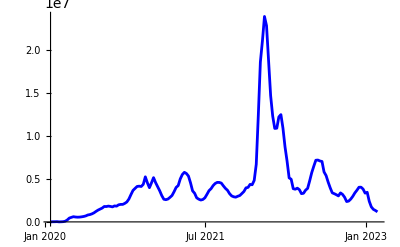

```mathematica
ListPlot[Transpose[{dates,cases}],Joined->True,PlotStyle->Blue,Ticks->{xaxis,Automatic},PlotRange->All]
```

### Recombinants - weekly

#### Entering rec data

From https://github.com/jeromekelleher/sc2ts-paper/blob/main/data/recombinants.csv (25 August 2025):

```mathematica
rec=Import["/Users/otto/Dropbox/COVID19/Recombinants/sc2ts/GlobalTrends/recombinants25August2025.csv","CSV"];
```

```mathematica
recheader=rec[[1]]
```

{recombinant,sample_id,num_descendant_samples,num_samples,distinct_sample_pango,interval_left,interval_right,num_mutations,Viridian_amplicon_scheme,Artic_primer_version,date_added,group_id,group_size,recombinant_pango,recombinant_scorpio,recombinant_time,recombinant_date,sample,sample_pango,sample_scorpio,sample_time,sample_date,parent_left,parent_left_pango,parent_left_scorpio,parent_left_time,parent_left_date,parent_right,parent_right_pango,parent_right_scorpio,parent_right_time,parent_right_date,oldest_child,oldest_child_pango,oldest_child_scorpio,oldest_child_time,oldest_child_date,parent_mrca,parent_mrca_pango,parent_mrca_scorpio,parent_mrca_time,parent_mrca_date,is_rebar_recombinant,parent_pangonet_distance,net_min_supporting_loci_lft,net_min_supporting_loci_rgt,net_min_supporting_loci_lft_rgt_ge_4,k1000_muts}

Dropping the header

```mathematica
rec=Drop[rec,1];
```

```mathematica
Length[rec]
```

855

```mathematica
calrecdates=rec[[2;;All,Position[recheader,"recombinant_date"][[1,1]]]];
```

Rounding the dates to the week (starting at 1):

```mathematica
recdates=Table[1+Floor[curdate[calrecdates[[i]]],7],{i,1,Length[calrecdates]}];
```

Gathering the dates together with more than one inferred recombination event:

```mathematica
recevents=Sort[Tally[recdates]]
```

{{57,1},{162,1},{176,1},{218,1},{239,2},{253,2},{260,2},{274,1},{323,2},{330,1},{344,1},{351,1},{358,3},{365,1},{372,1},{379,1},{386,1},{393,2},{400,2},{407,1},{421,1},{428,3},{442,3},{449,2},{463,1},{470,1},{477,1},{484,1},{505,1},{512,5},{519,4},{526,6},{533,6},{540,11},{547,17},{554,15},{561,9},{568,19},{575,21},{582,20},{589,16},{596,11},{603,20},{610,23},{617,34},{624,47},{631,37},{638,33},{645,12},{652,24},{659,15},{666,19},{673,21},{680,14},{687,11},{694,2},{701,4},{708,2},{715,6},{722,8},{729,11},{736,12},{743,7},{750,18},{757,16},{764,18},{771,14},{778,17},{785,6},{792,8},{799,7},{806,3},{813,2},{820,2},{827,2},{834,1},{848,6},{855,4},{862,4},{869,9},{876,10},{883,14},{890,15},{897,3},{904,8},{911,7},{918,7},{925,7},{932,9},{939,4},{946,6},{953,9},{960,7},{967,7},{974,6},{981,4},{988,3},{995,3},{1002,3},{1009,2},{1016,3},{1037,3},{1044,3},{1051,1},{1058,2},{1065,1},{1079,1},{1086,4},{1100,1}}

Adding zeros into the table for plotting:

```mathematica
recevents=Table[temp=Flatten[Select[recevents,#[[1]]==ii&]];If[Length[temp]>0,temp,{ii,0}],{ii,1,Max[dates],7}];
```

```mathematica
recdates=recevents[[All,1]];
```

We’ll end the dates on the last observed recombinant (case numbers continue for another month):

```mathematica
{Max[recevents[[All,1]]],Max[dates]}
```

{1114,1114}

```mathematica
Max[calrecdates]
```

Wed 25 Jan 2023

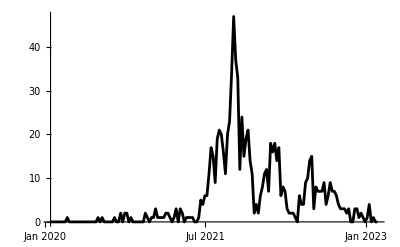

```mathematica
ListPlot[recevents,Joined->True,PlotStyle->Black,Ticks->{xaxis,Automatic},PlotRange->All]
```

Cases (blue) and recombination events (black), both scaled to their maxima:

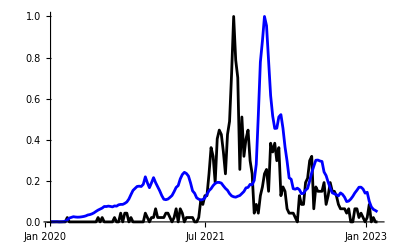

```mathematica
Show[
ListPlot[Transpose[{recevents[[All,1]],recevents[[All,2]]/Max[recevents[[All,2]]]}],Joined->True,PlotStyle->Black,Ticks->{xaxis,Automatic},PlotRange->All],
ListPlot[Transpose[{dates,cases/Max[cases]}],Joined->True,PlotStyle->Blue,Ticks->{xaxis,Automatic},PlotRange->All]
]
```

#### Shaded by variant

From https://github.com/jeromekelleher/sc2ts-paper/blob/main/arg_postprocessing/sc2ts_v1_2023-02-21_samples.csv (25 August 2025)

```mathematica
var=Import["/Users/otto/Dropbox/COVID19/Recombinants/sc2ts/GlobalTrends/sc2ts_v1_2023-02-21_samples25August2025.csv","CSV"];
```

```mathematica
varheader=var[[1]]
```

{Column1,date,exact_matches,mean_hmm_cost,median_hmm_cost,rejected,scorpio,total,total_hmm_cost,inserted}

Removing header and dates before and after the time period:

```mathematica
datepos=Position[varheader,"date"][[1,1]];
```

```mathematica
var=Select[var[[2;;All]],(curdate[#[[datepos]]]≥curdate[startafter])&&(curdate[#[[datepos]]]≤curdate[endatdate])&];
```

Eliminating internal nodes with no exact matches:

```mathematica
var=Select[var,#[[Position[varheader,"exact_matches"][[1,1]]]]>0&];
```

Renaming “.” as Pre-Alpha and collecting labels:

```mathematica
var[[All,Position[varheader,"scorpio"][[1,1]]]]=var[[All,Position[varheader,"scorpio"][[1,1]]]]/."."->"Pre-Alpha";
```

```mathematica
types=DeleteDuplicates[var[[All,Position[varheader,"scorpio"][[1,1]]]]]
```

{Pre-Alpha,Alpha (B.1.1.7-like),Beta (B.1.351-like),Epsilon (B.1.429-like),Epsilon (B.1.427-like),A.23.1-like,B.1.1.7-like+E484K,A.23.1-like+E484K,Gamma (P.1-like),Eta (B.1.525-like),B.1.1.318-like,Zeta (P.2-like),Iota (B.1.526-like),B.1.617.1-like,Delta (B.1.617.2-like),Mu (B.1.621-like),Lambda (C.37-like),Delta (AY.4-like),Delta (B.1.617.2-like) +K417N,AV.1-like,Delta (AY.4.2-like),Omicron (BA.1-like),Omicron (BA.2-like),Probable Omicron (BA.1-like),Omicron (Unassigned),Omicron (XE-like),Omicron (BA.4-like),Omicron (BA.5-like),Omicron (XBB-like),Omicron (XBB.1-like),Omicron (XBB.1.5-like)}

Choosing colors from Duotang’s list:

```mathematica
colors=Import["/Users/otto/Dropbox/COVID19/Recombinants/sc2ts/GlobalTrends/vocvoi.csv","CSV"];
```

Use this code to change the colors:
https://mathematica.stackexchange.com/questions/18495/how-to-convert-a-hex-color-string-to-rgbcolor

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&
```

RGBColor@@IntegerDigits[ToExpression[StringReplace[#1,#→16^^]],256,3]/255.&

```mathematica
colortab=Table[hexToRGB[colors[[i,2]]],{i,2,Length[colors]}]
```

{RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.6980392156862745, 0.611764705882353, 0.44313725490196076],RGBColor[0.9411764705882353, 0.5490196078431373, 0.22745098039215686],RGBColor[1., 0.6509803921568628, 0.16862745098039217],RGBColor[0.8862745098039215, 0.2980392156862745, 0.],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0., 0., 1.],RGBColor[0.4156862745098039, 0.5372549019607843, 0.6549019607843137],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.4588235294117647, 0.5058823529411764, 0.4196078431372549],RGBColor[0., 0.39215686274509803, 0.],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824],RGBColor[1., 0.8470588235294118, 0.34509803921568627],RGBColor[1., 1., 0.],RGBColor[0.27058823529411763, 0.7137254901960784, 0.9529411764705882],RGBColor[0.5607843137254902, 0.8274509803921568, 0.9529411764705882],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.8549019607843137, 0.9411764705882353, 1.],RGBColor[0.5450980392156862, 0., 0.],RGBColor[1., 0., 0.],RGBColor[0.5450980392156862, 0., 0.],RGBColor[0.5607843137254902, 0., 0.],RGBColor[0.5607843137254902, 0., 0.],RGBColor[0.7372549019607844, 0.32941176470588235, 0.29411764705882354],RGBColor[0.8, 0.4, 1.],RGBColor[0., 0.2980392156862745, 0.4588235294117647],RGBColor[0., 0.2980392156862745, 0.4588235294117647],RGBColor[0., 0.2980392156862745, 0.4588235294117647]}

All weeks:

```mathematica
Max[dates]
```

1114

```mathematica
vardates=Table[i,{i,1,Max[dates],7}]
```

{1,8,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127,134,141,148,155,162,169,176,183,190,197,204,211,218,225,232,239,246,253,260,267,274,281,288,295,302,309,316,323,330,337,344,351,358,365,372,379,386,393,400,407,414,421,428,435,442,449,456,463,470,477,484,491,498,505,512,519,526,533,540,547,554,561,568,575,582,589,596,603,610,617,624,631,638,645,652,659,666,673,680,687,694,701,708,715,722,729,736,743,750,757,764,771,778,785,792,799,806,813,820,827,834,841,848,855,862,869,876,883,890,897,904,911,918,925,932,939,946,953,960,967,974,981,988,995,1002,1009,1016,1023,1030,1037,1044,1051,1058,1065,1072,1079,1086,1093,1100,1107,1114}

Gathering all variants by week (note that we must multiply by the number observed on a day, “exact_matches”):

```mathematica
Clear[temp,varnum]
For[ii=1,ii≤Length[types],ii++,
temp=Select[var,#[[Position[varheader,"scorpio"][[1,1]]]]==types[[ii]]&];
For[jj=1;temp2={},jj≤Length[temp],jj++,
day = temp[[jj,Position[varheader,"date"][[1,1]]]];
week=1+Floor[curdate[day],7];
temp2=AppendTo[temp2,{week, temp[[jj,Position[varheader,"exact_matches"][[1,1]]]]}];
];
temp4=Table[temp3=Select[temp2,#[[1]]==i&];If[Length[temp3]>0,{i,Total[temp3[[All,2]]]},{i,0}],{i,1,Max[dates],7}];
If[Transpose[temp4][[1]]!=vardates,Print["error"]];
varnum[ii]=Transpose[temp4][[2]]
]
```

Number of samples by type:

```mathematica
{Table[colortab[[i]],{i,1,Length[types]}],types,Total[Transpose[Table[varnum[i],{i,1,Length[types]}]]]}//Transpose//TableForm
```

RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Pre-Alpha | 81491
RGBColor[0.6980392156862745, 0.611764705882353, 0.44313725490196076] | Alpha (B.1.1.7-like) | 165181
RGBColor[0.9411764705882353, 0.5490196078431373, 0.22745098039215686] | Beta (B.1.351-like) | 826
RGBColor[1., 0.6509803921568628, 0.16862745098039217] | Epsilon (B.1.429-like) | 2072
RGBColor[0.8862745098039215, 0.2980392156862745, 0.] | Epsilon (B.1.427-like) | 1367
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | A.23.1-like | 29
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | B.1.1.7-like+E484K | 111
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | A.23.1-like+E484K | 25
RGBColor[0., 0., 1.] | Gamma (P.1-like) | 1642
RGBColor[0.4156862745098039, 0.5372549019607843, 0.6549019607843137] | Eta (B.1.525-like) | 223
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | B.1.1.318-like | 396
RGBColor[0.4588235294117647, 0.5058823529411764, 0.4196078431372549] | Zeta (P.2-like) | 93
RGBColor[0., 0.39215686274509803, 0.] | Iota (B.1.526-like) | 3866
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | B.1.617.1-like | 127
RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824] | Delta (B.1.617.2-like) | 234228
RGBColor[1., 0.8470588235294118, 0.34509803921568627] | Mu (B.1.621-like) | 471
RGBColor[1., 1., 0.] | Lambda (C.37-like) | 68
RGBColor[0.27058823529411763, 0.7137254901960784, 0.9529411764705882] | Delta (AY.4-like) | 294486
RGBColor[0.5607843137254902, 0.8274509803921568, 0.9529411764705882] | Delta (B.1.617.2-like) +K417N | 481
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | AV.1-like | 85
RGBColor[0.8549019607843137, 0.9411764705882353, 1.] | Delta (AY.4.2-like) | 50560
RGBColor[0.5450980392156862, 0., 0.] | Omicron (BA.1-like) | 167123
RGBColor[1., 0., 0.] | Omicron (BA.2-like) | 182747
RGBColor[0.5450980392156862, 0., 0.] | Probable Omicron (BA.1-like) | 5
RGBColor[0.5607843137254902, 0., 0.] | Omicron (Unassigned) | 118
RGBColor[0.5607843137254902, 0., 0.] | Omicron (XE-like) | 678
RGBColor[0.7372549019607844, 0.32941176470588235, 0.29411764705882354] | Omicron (BA.4-like) | 8253
RGBColor[0.8, 0.4, 1.] | Omicron (BA.5-like) | 54003
RGBColor[0., 0.2980392156862745, 0.4588235294117647] | Omicron (XBB-like) | 103
RGBColor[0., 0.2980392156862745, 0.4588235294117647] | Omicron (XBB.1-like) | 189
RGBColor[0., 0.2980392156862745, 0.4588235294117647] | Omicron (XBB.1.5-like) | 987

Limiting the above to those with ≥1000

```mathematica
Select[{Table[colortab[[i]],{i,1,Length[types]}],types,Total[Transpose[Table[varnum[i],{i,1,Length[types]}]]]}//Transpose,#[[3]]≥1000&]//TableForm
```

RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Pre-Alpha | 81491
RGBColor[0.6980392156862745, 0.611764705882353, 0.44313725490196076] | Alpha (B.1.1.7-like) | 165181
RGBColor[1., 0.6509803921568628, 0.16862745098039217] | Epsilon (B.1.429-like) | 2072
RGBColor[0.8862745098039215, 0.2980392156862745, 0.] | Epsilon (B.1.427-like) | 1367
RGBColor[0., 0., 1.] | Gamma (P.1-like) | 1642
RGBColor[0., 0.39215686274509803, 0.] | Iota (B.1.526-like) | 3866
RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824] | Delta (B.1.617.2-like) | 234228
RGBColor[0.27058823529411763, 0.7137254901960784, 0.9529411764705882] | Delta (AY.4-like) | 294486
RGBColor[0.8549019607843137, 0.9411764705882353, 1.] | Delta (AY.4.2-like) | 50560
RGBColor[0.5450980392156862, 0., 0.] | Omicron (BA.1-like) | 167123
RGBColor[1., 0., 0.] | Omicron (BA.2-like) | 182747
RGBColor[0.7372549019607844, 0.32941176470588235, 0.29411764705882354] | Omicron (BA.4-like) | 8253
RGBColor[0.8, 0.4, 1.] | Omicron (BA.5-like) | 54003

```mathematica
filltab=Join[{1->{Axis,colortab[[1]]}},Table[i->{{i-1},colortab[[i]]},{i,2,Length[types]}]]
```

{1→{Axis,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},2→{{1},RGBColor[0.6980392156862745, 0.611764705882353, 0.44313725490196076]},3→{{2},RGBColor[0.9411764705882353, 0.5490196078431373, 0.22745098039215686]},4→{{3},RGBColor[1., 0.6509803921568628, 0.16862745098039217]},5→{{4},RGBColor[0.8862745098039215, 0.2980392156862745, 0.]},6→{{5},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},7→{{6},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},8→{{7},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},9→{{8},RGBColor[0., 0., 1.]},10→{{9},RGBColor[0.4156862745098039, 0.5372549019607843, 0.6549019607843137]},11→{{10},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},12→{{11},RGBColor[0.4588235294117647, 0.5058823529411764, 0.4196078431372549]},13→{{12},RGBColor[0., 0.39215686274509803, 0.]},14→{{13},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},15→{{14},RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824]},16→{{15},RGBColor[1., 0.8470588235294118, 0.34509803921568627]},17→{{16},RGBColor[1., 1., 0.]},18→{{17},RGBColor[0.27058823529411763, 0.7137254901960784, 0.9529411764705882]},19→{{18},RGBColor[0.5607843137254902, 0.8274509803921568, 0.9529411764705882]},20→{{19},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},21→{{20},RGBColor[0.8549019607843137, 0.9411764705882353, 1.]},22→{{21},RGBColor[0.5450980392156862, 0., 0.]},23→{{22},RGBColor[1., 0., 0.]},24→{{23},RGBColor[0.5450980392156862, 0., 0.]},25→{{24},RGBColor[0.5607843137254902, 0., 0.]},26→{{25},RGBColor[0.5607843137254902, 0., 0.]},27→{{26},RGBColor[0.7372549019607844, 0.32941176470588235, 0.29411764705882354]},28→{{27},RGBColor[0.8, 0.4, 1.]},29→{{28},RGBColor[0., 0.2980392156862745, 0.4588235294117647]},30→{{29},RGBColor[0., 0.2980392156862745, 0.4588235294117647]},31→{{30},RGBColor[0., 0.2980392156862745, 0.4588235294117647]}}

Cumulative plots, first based on the number of lineages in the ARG each week (x1000) relative to case numbers in the Veridian dataset:

```mathematica
Clear[cumvarnum]
For[ii=1,ii≤Length[types],ii++,
cumvarnum[ii]=Sum[varnum[j],{j,1,ii}]
]
```

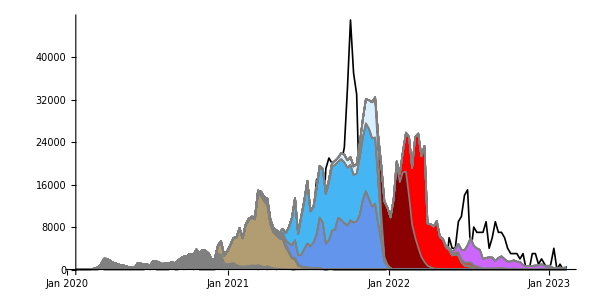

```mathematica
Show[
ListPlot[Transpose[{recevents[[All,1]],1000*recevents[[All,2]]}],Joined->True,PlotStyle->{Thickness[0.002],Black},PlotRange->All],
ListPlot[Table[Transpose[{vardates,cumvarnum[i]}],{i,1,Length[types]}],Joined->True,PlotRange->All,PlotStyle->{{Thickness[0.002],Gray}},
Filling->filltab,AspectRatio->1/2,Ticks->{xaxis,Automatic},ImageSize->600],
AspectRatio->1/2,Ticks->{xaxis,Automatic},ImageSize->600
]
```

Normalizing to the number of samples per day:

```mathematica
Table[normcumvar[i]=cumvarnum[i]/cumvarnum[Length[types]],{i,1,Length[types]}];
```

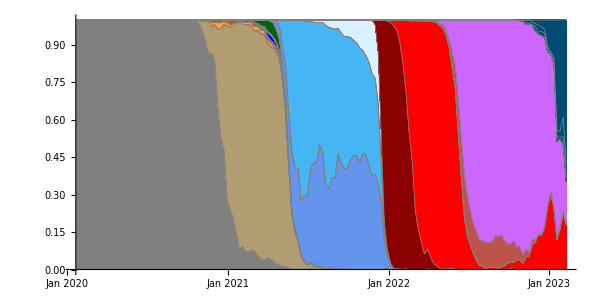

```mathematica
ListPlot[Table[Transpose[{vardates,normcumvar[i]}],{i,1,Length[types]}],Joined->True,PlotRange->All,PlotStyle->{{Thickness[0.001],Gray}},
Filling->filltab,AspectRatio->1/2,Ticks->{xaxis,Automatic},ImageSize->600]
```

Now with the height of the coloured curves given by the Johns Hopkins’ case database:

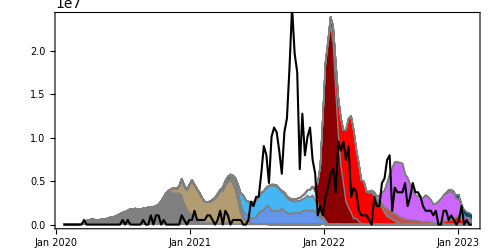

```mathematica
Show[
ListPlot[Table[Transpose[{vardates,cases*normcumvar[i]}],{i,1,Length[types]}],Joined->True,PlotRange->All,PlotStyle->{{Thickness[0.002],Gray}},
Filling->filltab,AspectRatio->1/2],
ListPlot[Transpose[{recevents[[All,1]],Max[cases]/45*recevents[[All,2]]}],Joined->True,PlotStyle->{Thickness[0.003],Black},PlotRange->All],
AspectRatio->1/2,Frame->True, FrameTicks->{{Automatic,Table[{i/45 2.5 10^7,i},{i,0,45,5}]},{xaxis,None}},ImageSize->500
]
```

We ask which single predictor best predicts the number of recombinant events (cases, het, cases*het, cases^2, cases^2*het). The interest in cases^2 stems from the possibility that double infections may rise with the square of the contact rates with other infected individuals. We do not assume an intercept at 0 because the case numbers are not well estimated, so we do not force the intercept.

The expected heterozygosity on each day (1-∑_(i=1)^types p_i⟦j⟧):

```mathematica
tabHET=Table[1-Sum[((varnum[i][[j]])/Sum[varnum[ii][[j]],{ii,1,Length[types]}])^2,{i,1,Length[types]}],{j,1,Length[vardates]}]//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0015859,0.029787,0.0844168,0.155738,0.235175,0.238074,0.283327,0.481955,0.530935,0.517847,0.438983,0.409986,0.358212,0.272817,0.168631,0.201216,0.167026,0.169117,0.193401,0.221576,0.184045,0.193577,0.176784,0.255076,0.275425,0.268059,0.282912,0.320406,0.438757,0.578568,0.663934,0.615353,0.565937,0.557605,0.424168,0.443706,0.435941,0.515434,0.521122,0.51471,0.528812,0.517627,0.476402,0.48109,0.508894,0.508626,0.533312,0.54645,0.55206,0.553049,0.561131,0.572677,0.579359,0.593422,0.599307,0.610614,0.627143,0.646408,0.659887,0.721428,0.67203,0.324497,0.156345,0.0689702,0.0503037,0.0792901,0.161124,0.288285,0.409636,0.497195,0.496845,0.369745,0.275953,0.20482,0.123811,0.158145,0.105758,0.0618874,0.0517459,0.0515441,0.0702262,0.115943,0.202917,0.330848,0.430851,0.583501,0.616387,0.541698,0.458213,0.381853,0.309484,0.263385,0.208677,0.207391,0.192685,0.194749,0.201511,0.239385,0.227817,0.243187,0.210358,0.187047,0.190422,0.207518,0.179605,0.176376,0.12934,0.187714,0.166687,0.259765,0.283233,0.339115,0.340998,0.399922,0.553919,0.584308,0.587235,0.64168,0.645978,0.715251,0.60655}

(1) CASES

```mathematica
lm=LinearModelFit[Transpose[{cases,recevents[[All,2]]}],{x},x];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.0657882

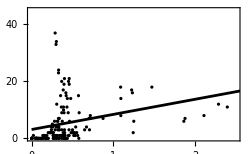

```mathematica
Show[
ListPlot[Transpose[{cases,recevents[[All,2]]}],PlotStyle->Black],
Plot[Normal[lm],{x,0,10^8},PlotStyle->Black],
PlotRange->{{0,2.5 10^7},{0,45}},AxesOrigin->{0,0},
Ticks->{Automatic,Table[i,{i,0,45,5}]},
ImageSize->250,Frame->True
]
```

(2) HETEROZYGOSITY

```mathematica
lm=LinearModelFit[Transpose[{tabHET,recevents[[All,2]]}],{x},x];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.265017

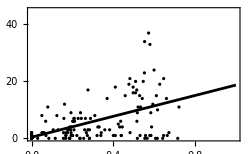

```mathematica
Show[
ListPlot[Transpose[{tabHET,recevents[[All,2]]}],PlotStyle->Black],
Plot[Normal[lm],{x,0,1},PlotStyle->Black],
PlotRange->{{0,1},{0,45}},AxesOrigin->{0,0},
Ticks->{Automatic,Table[i,{i,0,45,5}]},
ImageSize->250,Frame->True
]
```

(3) CASES*HET

```mathematica
lm=LinearModelFit[Transpose[{cases*tabHET,recevents[[All,2]]}],{x},x];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.269222

Plotting the product of case numbers and expected heterozygosity (the best single estimator):

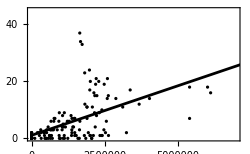

```mathematica
Show[
ListPlot[Transpose[{cases*tabHET,recevents[[All,2]]}],PlotStyle->Black],
Plot[Normal[lm],{x,0,10^7},PlotStyle->Black],
PlotRange->{{0,0.7 10^7},{0,45}},AxesOrigin->{0,0},
FrameTicks->{Automatic,Table[i,{i,0,45,5}],None,None},
ImageSize->250,Frame->True
]
```

(4) CASES^2*HET

```mathematica
lm=LinearModelFit[Transpose[{cases,recevents[[All,2]]}],{x^2},x];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.02593

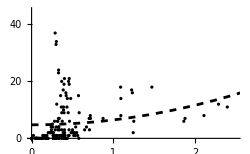

```mathematica
Show[
ListPlot[Transpose[{cases,recevents[[All,2]]}],PlotStyle->Black],
Plot[Normal[lm],{x,0,10^8},PlotStyle->{Dashed,Black}],
PlotRange->{{0,2.5 10^7},{0,45}},AxesOrigin->{0,0},
Ticks->{Automatic,Table[i,{i,0,45,5}]},
ImageSize->250
]
```

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x^2 y},{x,y}];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.0979461

Finally, we consider more traditional model fits allowing cases (and/or squared case numbers), het, and their interaction, but this approach focuses more on what factors best fit the data, not which predictor is best:

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,y,x y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.311731

There is no evidence for an improvement in fit when the case numbers are multiplied by heterozygosity, given that both variables are already included in the model, so dropping this term:

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.305601

```mathematica
Show[
ListPointPlot3D[Transpose[{cases,tabHET,recevents[[All,2]]}],PlotStyle->Black],
Plot3D[Normal[lm],{x,0,10^8},{y,0,1},PlotStyle->RGBColor[0.4,0.9,0.4,0.2]],
PlotRange->{{0,2.5 10^7},{0,1},{0,45}},AxesOrigin->{0,0,0},
Ticks->{Automatic,Automatic,Table[i,{i,0,45,5}]},
ImageSize->350
]
```

-Graphics3D-

Adding cases squared to the fit (plus interactions)

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,x^2,y,x y,x^2 y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.312467

Again, there is no evidence for an improvement in fit when the case numbers (or squared case numbers) are multiplied by heterozygosity given that both terms are present, so dropping these terms:

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,x^2,y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.301345

```mathematica
Show[
ListPointPlot3D[Transpose[{cases,tabHET,recevents[[All,2]]}],PlotStyle->Black],
Plot3D[Normal[lm],{x,0,10^8},{y,0,1},PlotStyle->RGBColor[0.4,0.9,0.4,0.2]],
PlotRange->{{0,2.5 10^7},{0,1},{0,45}},AxesOrigin->{0,0,0},
Ticks->{Automatic,Automatic,Table[i,{i,0,45,5}]},
ImageSize->350
]
```

-Graphics3D-

Overall, the linear model fits generally show that both lineage diversity (“expected heterozygosity”) and case numbers are important variables in the model, but the exact functional relationship is unclear beyond the linear terms.

### Recombinants - weekly (net_min_supporting_loci_lft_rgt_ge_4 = True)

#### Entering rec data

From https://github.com/jeromekelleher/sc2ts-paper/blob/main/data/recombinants.csv (25 August 2025):

```mathematica
rec=Import["/Users/otto/Dropbox/COVID19/Recombinants/sc2ts/GlobalTrends/recombinants25August2025.csv","CSV"];
```

```mathematica
recheader=rec[[1]]
```

{recombinant,sample_id,num_descendant_samples,num_samples,distinct_sample_pango,interval_left,interval_right,num_mutations,Viridian_amplicon_scheme,Artic_primer_version,date_added,group_id,group_size,recombinant_pango,recombinant_scorpio,recombinant_time,recombinant_date,sample,sample_pango,sample_scorpio,sample_time,sample_date,parent_left,parent_left_pango,parent_left_scorpio,parent_left_time,parent_left_date,parent_right,parent_right_pango,parent_right_scorpio,parent_right_time,parent_right_date,oldest_child,oldest_child_pango,oldest_child_scorpio,oldest_child_time,oldest_child_date,parent_mrca,parent_mrca_pango,parent_mrca_scorpio,parent_mrca_time,parent_mrca_date,is_rebar_recombinant,parent_pangonet_distance,net_min_supporting_loci_lft,net_min_supporting_loci_rgt,net_min_supporting_loci_lft_rgt_ge_4,k1000_muts}

```mathematica
rec=Select[rec,#[[Position[recheader,"net_min_supporting_loci_lft_rgt_ge_4"][[1,1]]]]==True&];
```

```mathematica
Length[%]
```

356

```mathematica
calrecdates=rec[[2;;All,Position[recheader,"recombinant_date"][[1,1]]]];
```

Rounding the dates to the week (starting at 1):

```mathematica
recdates=Table[1+Floor[curdate[calrecdates[[i]]],7],{i,1,Length[calrecdates]}];
```

Gathering the dates together with more than one inferred recombination event:

```mathematica
recevents=Sort[Tally[recdates]]
```

{{57,1},{162,1},{176,1},{218,1},{239,2},{253,1},{260,2},{274,1},{323,2},{330,1},{344,1},{351,1},{358,3},{365,1},{372,1},{393,1},{407,1},{442,2},{449,1},{463,1},{477,1},{505,1},{519,1},{526,2},{533,2},{540,7},{547,10},{554,7},{561,4},{568,5},{575,4},{582,8},{589,2},{596,5},{603,3},{610,4},{617,5},{624,5},{631,6},{638,5},{645,2},{652,3},{659,1},{666,3},{673,6},{680,4},{687,5},{694,2},{701,1},{708,2},{715,2},{722,6},{729,7},{736,8},{743,4},{750,4},{757,2},{764,4},{771,6},{778,6},{785,3},{792,2},{799,2},{806,2},{827,2},{848,5},{855,2},{862,4},{869,7},{876,10},{883,13},{890,15},{897,3},{904,6},{911,6},{918,6},{925,6},{932,7},{939,3},{946,5},{953,7},{960,7},{967,6},{974,5},{981,3},{988,3},{995,2},{1002,3},{1009,2},{1016,3},{1037,3},{1044,3},{1051,1},{1058,1},{1065,1},{1079,1},{1086,3},{1100,1}}

Adding zeros into the table for plotting:

```mathematica
recevents=Table[temp=Flatten[Select[recevents,#[[1]]==ii&]];If[Length[temp]>0,temp,{ii,0}],{ii,1,Max[dates],7}];
```

```mathematica
recdates=recevents[[All,1]];
```

We’ll end the dates on the last observed recombinant (case numbers continue for another month):

```mathematica
{Max[recevents[[All,1]]],Max[dates]}
```

{1114,1114}

```mathematica
Max[calrecdates]
```

Wed 25 Jan 2023

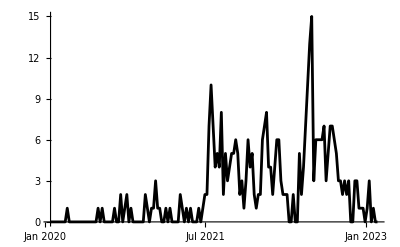

```mathematica
ListPlot[recevents,Joined->True,PlotStyle->Black,Ticks->{xaxis,Automatic},PlotRange->All]
```

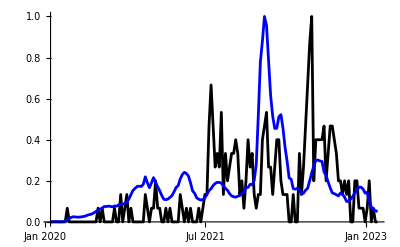

```mathematica
Show[
ListPlot[Transpose[{recevents[[All,1]],recevents[[All,2]]/Max[recevents[[All,2]]]}],Joined->True,PlotStyle->Black,Ticks->{xaxis,Automatic},PlotRange->All],
ListPlot[Transpose[{dates,cases/Max[cases]}],Joined->True,PlotStyle->Blue,Ticks->{xaxis,Automatic},PlotRange->All]
]
```

#### Shaded by variant

From https://github.com/jeromekelleher/sc2ts-paper/blob/main/arg_postprocessing/sc2ts_v1_2023-02-21_samples.csv (25 August 2025)

```mathematica
var=Import["/Users/otto/Dropbox/COVID19/Recombinants/sc2ts/GlobalTrends/sc2ts_v1_2023-02-21_samples25August2025.csv","CSV"];
```

```mathematica
varheader=var[[1]]
```

{Column1,date,exact_matches,mean_hmm_cost,median_hmm_cost,rejected,scorpio,total,total_hmm_cost,inserted}

Removing header and dates before and after the time period:

```mathematica
datepos=Position[varheader,"date"][[1,1]];
```

```mathematica
var=Select[var[[2;;All]],(curdate[#[[datepos]]]≥curdate[startafter])&&(curdate[#[[datepos]]]≤curdate[endatdate])&];
```

Eliminating internal nodes with no exact matches:

```mathematica
var=Select[var,#[[Position[varheader,"exact_matches"][[1,1]]]]>0&];
```

Renaming “.” as Pre-Alpha and collecting labels:

```mathematica
var[[All,Position[varheader,"scorpio"][[1,1]]]]=var[[All,Position[varheader,"scorpio"][[1,1]]]]/."."->"Pre-Alpha";
```

```mathematica
types=DeleteDuplicates[var[[All,Position[varheader,"scorpio"][[1,1]]]]]
```

{Pre-Alpha,Alpha (B.1.1.7-like),Beta (B.1.351-like),Epsilon (B.1.429-like),Epsilon (B.1.427-like),A.23.1-like,B.1.1.7-like+E484K,A.23.1-like+E484K,Gamma (P.1-like),Eta (B.1.525-like),B.1.1.318-like,Zeta (P.2-like),Iota (B.1.526-like),B.1.617.1-like,Delta (B.1.617.2-like),Mu (B.1.621-like),Lambda (C.37-like),Delta (AY.4-like),Delta (B.1.617.2-like) +K417N,AV.1-like,Delta (AY.4.2-like),Omicron (BA.1-like),Omicron (BA.2-like),Probable Omicron (BA.1-like),Omicron (Unassigned),Omicron (XE-like),Omicron (BA.4-like),Omicron (BA.5-like),Omicron (XBB-like),Omicron (XBB.1-like),Omicron (XBB.1.5-like)}

Choosing colors from Duotang’s list:

```mathematica
colors=Import["/Users/otto/Dropbox/COVID19/Recombinants/sc2ts/GlobalTrends/vocvoi.csv","CSV"];
```

Use this code to change the colors:
https://mathematica.stackexchange.com/questions/18495/how-to-convert-a-hex-color-string-to-rgbcolor

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&
```

RGBColor@@IntegerDigits[ToExpression[StringReplace[#1,#→16^^]],256,3]/255.&

```mathematica
colortab=Table[hexToRGB[colors[[i,2]]],{i,2,Length[colors]}]
```

{RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.6980392156862745, 0.611764705882353, 0.44313725490196076],RGBColor[0.9411764705882353, 0.5490196078431373, 0.22745098039215686],RGBColor[1., 0.6509803921568628, 0.16862745098039217],RGBColor[0.8862745098039215, 0.2980392156862745, 0.],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0., 0., 1.],RGBColor[0.4156862745098039, 0.5372549019607843, 0.6549019607843137],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.4588235294117647, 0.5058823529411764, 0.4196078431372549],RGBColor[0., 0.39215686274509803, 0.],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824],RGBColor[1., 0.8470588235294118, 0.34509803921568627],RGBColor[1., 1., 0.],RGBColor[0.27058823529411763, 0.7137254901960784, 0.9529411764705882],RGBColor[0.5607843137254902, 0.8274509803921568, 0.9529411764705882],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.8549019607843137, 0.9411764705882353, 1.],RGBColor[0.5450980392156862, 0., 0.],RGBColor[1., 0., 0.],RGBColor[0.5450980392156862, 0., 0.],RGBColor[0.5607843137254902, 0., 0.],RGBColor[0.5607843137254902, 0., 0.],RGBColor[0.7372549019607844, 0.32941176470588235, 0.29411764705882354],RGBColor[0.8, 0.4, 1.],RGBColor[0., 0.2980392156862745, 0.4588235294117647],RGBColor[0., 0.2980392156862745, 0.4588235294117647],RGBColor[0., 0.2980392156862745, 0.4588235294117647]}

All weeks:

```mathematica
Max[dates]
```

1114

```mathematica
vardates=Table[i,{i,1,Max[dates],7}]
```

{1,8,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127,134,141,148,155,162,169,176,183,190,197,204,211,218,225,232,239,246,253,260,267,274,281,288,295,302,309,316,323,330,337,344,351,358,365,372,379,386,393,400,407,414,421,428,435,442,449,456,463,470,477,484,491,498,505,512,519,526,533,540,547,554,561,568,575,582,589,596,603,610,617,624,631,638,645,652,659,666,673,680,687,694,701,708,715,722,729,736,743,750,757,764,771,778,785,792,799,806,813,820,827,834,841,848,855,862,869,876,883,890,897,904,911,918,925,932,939,946,953,960,967,974,981,988,995,1002,1009,1016,1023,1030,1037,1044,1051,1058,1065,1072,1079,1086,1093,1100,1107,1114}

Gathering all variants by week (note that we must multiply by the number observed on a day, “exact_matches”):

```mathematica
Clear[temp,varnum]
For[ii=1,ii≤Length[types],ii++,
temp=Select[var,#[[Position[varheader,"scorpio"][[1,1]]]]==types[[ii]]&];
For[jj=1;temp2={},jj≤Length[temp],jj++,
day = temp[[jj,Position[varheader,"date"][[1,1]]]];
week=1+Floor[curdate[day],7];
temp2=AppendTo[temp2,{week, temp[[jj,Position[varheader,"exact_matches"][[1,1]]]]}];
];
temp4=Table[temp3=Select[temp2,#[[1]]==i&];If[Length[temp3]>0,{i,Total[temp3[[All,2]]]},{i,0}],{i,1,Max[dates],7}];
If[Transpose[temp4][[1]]!=vardates,Print["error"]];
varnum[ii]=Transpose[temp4][[2]]
]
```

Number of samples by type:

```mathematica
{Table[colortab[[i]],{i,1,Length[types]}],types,Total[Transpose[Table[varnum[i],{i,1,Length[types]}]]]}//Transpose//TableForm
```

RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Pre-Alpha | 81491
RGBColor[0.6980392156862745, 0.611764705882353, 0.44313725490196076] | Alpha (B.1.1.7-like) | 165181
RGBColor[0.9411764705882353, 0.5490196078431373, 0.22745098039215686] | Beta (B.1.351-like) | 826
RGBColor[1., 0.6509803921568628, 0.16862745098039217] | Epsilon (B.1.429-like) | 2072
RGBColor[0.8862745098039215, 0.2980392156862745, 0.] | Epsilon (B.1.427-like) | 1367
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | A.23.1-like | 29
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | B.1.1.7-like+E484K | 111
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | A.23.1-like+E484K | 25
RGBColor[0., 0., 1.] | Gamma (P.1-like) | 1642
RGBColor[0.4156862745098039, 0.5372549019607843, 0.6549019607843137] | Eta (B.1.525-like) | 223
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | B.1.1.318-like | 396
RGBColor[0.4588235294117647, 0.5058823529411764, 0.4196078431372549] | Zeta (P.2-like) | 93
RGBColor[0., 0.39215686274509803, 0.] | Iota (B.1.526-like) | 3866
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | B.1.617.1-like | 127
RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824] | Delta (B.1.617.2-like) | 234228
RGBColor[1., 0.8470588235294118, 0.34509803921568627] | Mu (B.1.621-like) | 471
RGBColor[1., 1., 0.] | Lambda (C.37-like) | 68
RGBColor[0.27058823529411763, 0.7137254901960784, 0.9529411764705882] | Delta (AY.4-like) | 294486
RGBColor[0.5607843137254902, 0.8274509803921568, 0.9529411764705882] | Delta (B.1.617.2-like) +K417N | 481
RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | AV.1-like | 85
RGBColor[0.8549019607843137, 0.9411764705882353, 1.] | Delta (AY.4.2-like) | 50560
RGBColor[0.5450980392156862, 0., 0.] | Omicron (BA.1-like) | 167123
RGBColor[1., 0., 0.] | Omicron (BA.2-like) | 182747
RGBColor[0.5450980392156862, 0., 0.] | Probable Omicron (BA.1-like) | 5
RGBColor[0.5607843137254902, 0., 0.] | Omicron (Unassigned) | 118
RGBColor[0.5607843137254902, 0., 0.] | Omicron (XE-like) | 678
RGBColor[0.7372549019607844, 0.32941176470588235, 0.29411764705882354] | Omicron (BA.4-like) | 8253
RGBColor[0.8, 0.4, 1.] | Omicron (BA.5-like) | 54003
RGBColor[0., 0.2980392156862745, 0.4588235294117647] | Omicron (XBB-like) | 103
RGBColor[0., 0.2980392156862745, 0.4588235294117647] | Omicron (XBB.1-like) | 189
RGBColor[0., 0.2980392156862745, 0.4588235294117647] | Omicron (XBB.1.5-like) | 987

Limiting the above to those with ≥1000

```mathematica
Select[{Table[colortab[[i]],{i,1,Length[types]}],types,Total[Transpose[Table[varnum[i],{i,1,Length[types]}]]]}//Transpose,#[[3]]≥1000&]//TableForm
```

RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Pre-Alpha | 81491
RGBColor[0.6980392156862745, 0.611764705882353, 0.44313725490196076] | Alpha (B.1.1.7-like) | 165181
RGBColor[1., 0.6509803921568628, 0.16862745098039217] | Epsilon (B.1.429-like) | 2072
RGBColor[0.8862745098039215, 0.2980392156862745, 0.] | Epsilon (B.1.427-like) | 1367
RGBColor[0., 0., 1.] | Gamma (P.1-like) | 1642
RGBColor[0., 0.39215686274509803, 0.] | Iota (B.1.526-like) | 3866
RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824] | Delta (B.1.617.2-like) | 234228
RGBColor[0.27058823529411763, 0.7137254901960784, 0.9529411764705882] | Delta (AY.4-like) | 294486
RGBColor[0.8549019607843137, 0.9411764705882353, 1.] | Delta (AY.4.2-like) | 50560
RGBColor[0.5450980392156862, 0., 0.] | Omicron (BA.1-like) | 167123
RGBColor[1., 0., 0.] | Omicron (BA.2-like) | 182747
RGBColor[0.7372549019607844, 0.32941176470588235, 0.29411764705882354] | Omicron (BA.4-like) | 8253
RGBColor[0.8, 0.4, 1.] | Omicron (BA.5-like) | 54003

```mathematica
filltab=Join[{1->{Axis,colortab[[1]]}},Table[i->{{i-1},colortab[[i]]},{i,2,Length[types]}]]
```

{1→{Axis,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},2→{{1},RGBColor[0.6980392156862745, 0.611764705882353, 0.44313725490196076]},3→{{2},RGBColor[0.9411764705882353, 0.5490196078431373, 0.22745098039215686]},4→{{3},RGBColor[1., 0.6509803921568628, 0.16862745098039217]},5→{{4},RGBColor[0.8862745098039215, 0.2980392156862745, 0.]},6→{{5},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},7→{{6},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},8→{{7},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},9→{{8},RGBColor[0., 0., 1.]},10→{{9},RGBColor[0.4156862745098039, 0.5372549019607843, 0.6549019607843137]},11→{{10},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},12→{{11},RGBColor[0.4588235294117647, 0.5058823529411764, 0.4196078431372549]},13→{{12},RGBColor[0., 0.39215686274509803, 0.]},14→{{13},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},15→{{14},RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824]},16→{{15},RGBColor[1., 0.8470588235294118, 0.34509803921568627]},17→{{16},RGBColor[1., 1., 0.]},18→{{17},RGBColor[0.27058823529411763, 0.7137254901960784, 0.9529411764705882]},19→{{18},RGBColor[0.5607843137254902, 0.8274509803921568, 0.9529411764705882]},20→{{19},RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]},21→{{20},RGBColor[0.8549019607843137, 0.9411764705882353, 1.]},22→{{21},RGBColor[0.5450980392156862, 0., 0.]},23→{{22},RGBColor[1., 0., 0.]},24→{{23},RGBColor[0.5450980392156862, 0., 0.]},25→{{24},RGBColor[0.5607843137254902, 0., 0.]},26→{{25},RGBColor[0.5607843137254902, 0., 0.]},27→{{26},RGBColor[0.7372549019607844, 0.32941176470588235, 0.29411764705882354]},28→{{27},RGBColor[0.8, 0.4, 1.]},29→{{28},RGBColor[0., 0.2980392156862745, 0.4588235294117647]},30→{{29},RGBColor[0., 0.2980392156862745, 0.4588235294117647]},31→{{30},RGBColor[0., 0.2980392156862745, 0.4588235294117647]}}

Cumulative plots, first based on the number of lineages in the ARG each week (x1000) relative to case numbers in the Veridian dataset:

```mathematica
Clear[cumvarnum]
For[ii=1,ii≤Length[types],ii++,
cumvarnum[ii]=Sum[varnum[j],{j,1,ii}]
]
```

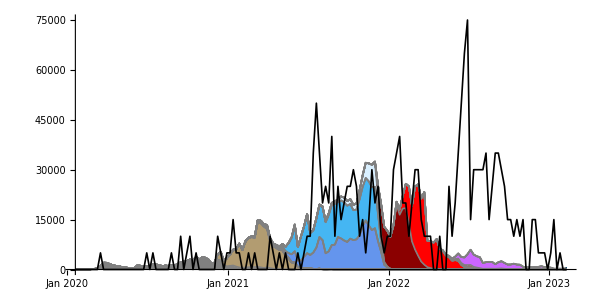

```mathematica
Show[
ListPlot[Table[Transpose[{vardates,cumvarnum[i]}],{i,1,Length[types]}],Joined->True,PlotRange->All,PlotStyle->{{Thickness[0.002],Gray}},
Filling->filltab,AspectRatio->1/2,Ticks->{xaxis,Automatic},ImageSize->600],
ListPlot[Transpose[{recevents[[All,1]],5000*recevents[[All,2]]}],Joined->True,PlotStyle->{Thickness[0.002],Black}],PlotRange->All,
AspectRatio->1/2,Ticks->{xaxis,Automatic},ImageSize->600
]
```

Normalizing to the number of samples per day:

```mathematica
Table[normcumvar[i]=cumvarnum[i]/cumvarnum[Length[types]],{i,1,Length[types]}];
```

```mathematica
ListPlot[Table[Transpose[{vardates,normcumvar[i]}],{i,1,Length[types]}],Joined->True,PlotRange->All,PlotStyle->{{Thickness[0.001],Gray}},
Filling->filltab,AspectRatio->1/2,Ticks->{xaxis,Automatic},ImageSize->600]
```

-Graphics-

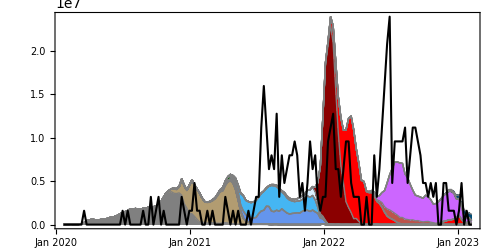

```mathematica
Show[
ListPlot[Table[Transpose[{vardates,cases*normcumvar[i]}],{i,1,Length[types]}],Joined->True,PlotRange->All,PlotStyle->{{Thickness[0.002],Gray}},
Filling->filltab,AspectRatio->1/2],
ListPlot[Transpose[{recevents[[All,1]],Max[cases]/15*recevents[[All,2]]}],Joined->True,PlotStyle->{Thickness[0.003],Black},PlotRange->All],
AspectRatio->1/2,Frame->True, FrameTicks->{{Automatic,Table[{i/15 2.5 10^7,i},{i,0,15,2}]},{xaxis,None}},ImageSize->500
]
```

We ask which single predictor best predicts the number of recombinant events (cases, het, cases*het, cases^2, cases^2*het). The interest in cases^2 stems from the possibility that double infections may rise with the square of the contact rates with other infected individuals. We do not assume an intercept at 0 because the case numbers are not well estimated, so we do not force the intercept.

The expected heterozygosity on each day (1-∑_(i=1)^types p_i⟦j⟧):

```mathematica
tabHET=Table[1-Sum[((varnum[i][[j]])/Sum[varnum[ii][[j]],{ii,1,Length[types]}])^2,{i,1,Length[types]}],{j,1,Length[vardates]}]//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0015859,0.029787,0.0844168,0.155738,0.235175,0.238074,0.283327,0.481955,0.530935,0.517847,0.438983,0.409986,0.358212,0.272817,0.168631,0.201216,0.167026,0.169117,0.193401,0.221576,0.184045,0.193577,0.176784,0.255076,0.275425,0.268059,0.282912,0.320406,0.438757,0.578568,0.663934,0.615353,0.565937,0.557605,0.424168,0.443706,0.435941,0.515434,0.521122,0.51471,0.528812,0.517627,0.476402,0.48109,0.508894,0.508626,0.533312,0.54645,0.55206,0.553049,0.561131,0.572677,0.579359,0.593422,0.599307,0.610614,0.627143,0.646408,0.659887,0.721428,0.67203,0.324497,0.156345,0.0689702,0.0503037,0.0792901,0.161124,0.288285,0.409636,0.497195,0.496845,0.369745,0.275953,0.20482,0.123811,0.158145,0.105758,0.0618874,0.0517459,0.0515441,0.0702262,0.115943,0.202917,0.330848,0.430851,0.583501,0.616387,0.541698,0.458213,0.381853,0.309484,0.263385,0.208677,0.207391,0.192685,0.194749,0.201511,0.239385,0.227817,0.243187,0.210358,0.187047,0.190422,0.207518,0.179605,0.176376,0.12934,0.187714,0.166687,0.259765,0.283233,0.339115,0.340998,0.399922,0.553919,0.584308,0.587235,0.64168,0.645978,0.715251,0.60655}

(1) CASES

```mathematica
lm=LinearModelFit[Transpose[{cases,recevents[[All,2]]}],{x},x];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.158943

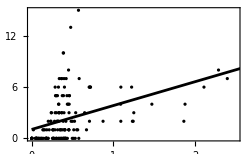

```mathematica
Show[
ListPlot[Transpose[{cases,recevents[[All,2]]}],PlotStyle->Black],
Plot[Normal[lm],{x,0,10^8},PlotStyle->Black],
PlotRange->{{0,2.5 10^7},{0,15}},AxesOrigin->{0,0},
FrameTicks->{Automatic,Table[i,{i,0,15,2}],None,None},
ImageSize->250,Frame->True
]
```

Testing p-value by randomization (all 10,000 had slopes of lower magnitude):

```mathematica
SeedRandom[9324];
For[jj=1;sig={0,0},jj≤10000,jj++,
tempcases=RandomSample[cases];
tempfit=LinearModelFit[Transpose[{cases,recevents[[All,2]]}],{x},x];
If[Abs[tempfit["BestFitParameters"][[2]]]>Abs[lm["BestFitParameters"][[2]]],sig=sig+{0,1},sig=sig+{1,0}]
]
sig/10000
```

{1,0}

(2) HETEROZYGOSITY

```mathematica
lm=LinearModelFit[Transpose[{tabHET,recevents[[All,2]]}],{x},x];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.146935

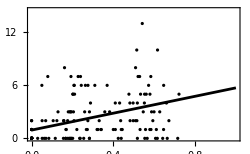

```mathematica
Show[
ListPlot[Transpose[{tabHET,recevents[[All,2]]}],PlotStyle->Black],
Plot[Normal[lm],{x,0,1},PlotStyle->Black],
PlotRange->{{0,1},{0,14.5}},AxesOrigin->{0,0},
FrameTicks->{Automatic,Table[i,{i,0,15,2}],None,None},
ImageSize->250,Frame->True
]
```

Testing p-value by randomization (all 10,000 had slopes of lower magnitude):

```mathematica
SeedRandom[1239];
For[jj=1;sig={0,0},jj≤10000,jj++,
tempcases=RandomSample[tabHET];
tempfit=LinearModelFit[Transpose[{tabHET,recevents[[All,2]]}],{x},x];
If[Abs[tempfit["BestFitParameters"][[2]]]>Abs[lm["BestFitParameters"][[2]]],sig=sig+{0,1},sig=sig+{1,0}]
]
sig/10000
```

{1,0}

(3) CASES*HET

```mathematica
lm=LinearModelFit[Transpose[{cases*tabHET,recevents[[All,2]]}],{x},x];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.237474

Plotting the product of case numbers and expected heterozygosity (the best single estimator):

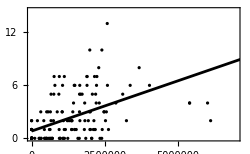

```mathematica
Show[
ListPlot[Transpose[{cases*tabHET,recevents[[All,2]]}],PlotStyle->Black],
Plot[Normal[lm],{x,0,10^7},PlotStyle->Black],
PlotRange->{{0,0.7 10^7},{0,14.5}},AxesOrigin->{0,0},
FrameTicks->{Automatic,Table[i,{i,0,15,2}],None,None},
ImageSize->250,Frame->True
]
```

Testing p-value by randomization (all 10,000 had slopes of lower magnitude):

```mathematica
SeedRandom[2323];
For[jj=1;sig={0,0},jj≤10000,jj++,
tempcases=RandomSample[cases*tabHET];
tempfit=LinearModelFit[Transpose[{cases*tabHET,recevents[[All,2]]}],{x},x];
If[Abs[tempfit["BestFitParameters"][[2]]]>Abs[lm["BestFitParameters"][[2]]],sig=sig+{0,1},sig=sig+{1,0}]
]
sig/10000
```

{1,0}

(4) CASES^2*HET

```mathematica
lm=LinearModelFit[Transpose[{cases,recevents[[All,2]]}],{x^2},x];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.0887058

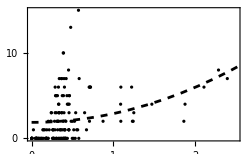

```mathematica
Show[
ListPlot[Transpose[{cases,recevents[[All,2]]}],PlotStyle->Black],
Plot[Normal[lm],{x,0,10^8},PlotStyle->{Dashed,Black}],
PlotRange->{{0,2.5 10^7},{0,15}},AxesOrigin->{0,0},
FrameTicks->{Automatic,Table[i,{i,0,15,5}],None,None},
ImageSize->250,Frame->True
]
```

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x^2 y},{x,y}];
lm["ParameterEstimates"]
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.11712

Finally, we consider more traditional model fits allowing cases (and/or squared case numbers), het, and their interaction, but this approach focuses more on what factors best fit the data, not which predictor is best:

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,y,x y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.273581

There is no evidence for an improvement in fit when the case numbers are multiplied by heterozygosity, given that both variables are already included in the model, so dropping this term:

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.275848

```mathematica
Show[
ListPointPlot3D[Transpose[{cases,tabHET,recevents[[All,2]]}],PlotStyle->Black],
Plot3D[Normal[lm],{x,0,10^8},{y,0,1},PlotStyle->RGBColor[0.4,0.9,0.4,0.2]],
PlotRange->{{0,2.5 10^7},{0,1},{0,45}},AxesOrigin->{0,0,0},
Ticks->{Automatic,Automatic,Table[i,{i,0,45,5}]},
ImageSize->350
]
```

-Graphics3D-

Adding cases squared to the fit (plus interactions)

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,x^2,y,x y,x^2 y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.300397

Again, there is no evidence for an improvement in fit when the case numbers are multiplied by heterozygosity given that both terms are present, so dropping this term:

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,x^2,y,x^2 y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.271403

The case numbers squared multiplied by heterozygosity is no longer significant, so dropping this term:

```mathematica
lm=LinearModelFit[Transpose[{cases,tabHET,recevents[[All,2]]}],{x,x^2,y},{x,y}];
lm["ANOVA"]
lm["AdjustedRSquared"]
```

0.274481

```mathematica
Show[
ListPointPlot3D[Transpose[{cases,tabHET,recevents[[All,2]]}],PlotStyle->Black],
Plot3D[Normal[lm],{x,0,10^8},{y,0,1},PlotStyle->RGBColor[0.4,0.9,0.4,0.2]],
PlotRange->{{0,2.5 10^7},{0,1},{0,45}},AxesOrigin->{0,0,0},
Ticks->{Automatic,Automatic,Table[i,{i,0,45,5}]},
ImageSize->350
]
```

-Graphics3D-

Overall, the linear model fits generally show that both lineage diversity (“expected heterozygosity”) and case numbers are important variables in the model, but the exact functional relationship is unclear beyond the linear terms.